```mathematica
Series[Sin[x],{x,0,5}]
```

x-x^3/6+x^5/120+O[x]^6

```mathematica
Series[(ϕ[x+a]-ϕ[x-a])/(2a),{a,0,5}]
```

ϕ'[x]+1/6 ϕ^(3)[x] a^2+1/120 ϕ^(5)[x] a^4+O[a]^6

```mathematica
Series[(ϕ[x+2a]-2ϕ[x+a]+ϕ[x])/a^2,{a,0,5}]
```

ϕ''[x]+ϕ^(3)[x] a+7/12 ϕ^(4)[x] a^2+1/4 ϕ^(5)[x] a^3+31/360 ϕ^(6)[x] a^4+1/40 ϕ^(7)[x] a^5+O[a]^6

```mathematica
Series[(ϕ[x+a]-2ϕ[x]+ϕ[x-a])/a^2,{a,0,5}]
```

ϕ''[x]+1/12 ϕ^(4)[x] a^2+1/360 ϕ^(6)[x] a^4+O[a]^6

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/student/compphys/week10

```mathematica
data=ReadList["!./laplace 200 1e-10 | awk '/^phi/{print $2, $3, $4}'",{Number,Number,Number}];
```

```mathematica
ListContourPlot[data,Contours->{5,25,50,75,95},ContourLabels->All,Epilog->Rectangle[{-.5,-.5},{.5,.5}]]
```

-Graphics-

```mathematica
datae=ReadList["!./laplace 100 1e-10 | awk '/^efield/{print $2, $3, $4, $5}'",{Number,Number,Number,Number}];
```

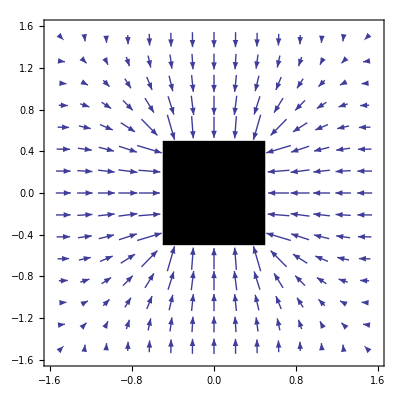

```mathematica
ListVectorPlot[datae,RegionFunction->Function[{x,y},Abs[x]>0.5||Abs[y]>0.5],Epilog->Rectangle[{-.5,-.5},{.5,.5}],VectorScale->0.06]
```